# Funciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2.(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
α=2 π/5;
ϕ=π;
t=1;
Unitary[θ,α,ϕ,t]
```

SparseArray[…]

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[HadamardMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Estado aleatorio

```mathematica
QubitState[θ_,ϕ_]:={Cos[θ/2] ,Exp[I ϕ] Sin[θ/2] }
```

```mathematica
ClearAll@RandomQubitState
```

```mathematica
RandomQubitState[seed_:Automatic,fixedθ_:Automatic,fixedϕ_:Automatic]:=Module[{θ,ϕ,u1,u2},If[seed=!=Automatic,SeedRandom[seed]];
u1=RandomReal[];u2=RandomReal[];θ=If[fixedθ===Automatic,ArcCos[2 u1-1],fixedθ];
ϕ=If[fixedϕ===Automatic,2 Pi u2,fixedϕ];
{θ,ϕ,Cos[θ/2],Exp[I ϕ] Sin[θ/2]}]
```

```mathematica
RandomQubitState[123]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
RandomQubitState[123,π/2.,Automatic]
```

{1.5708,6.14386,0.707107,0.700255-0.0981984 ⅈ}

```mathematica
RandomQubitState[123,Automatic,Automatic]
```

{1.65947,6.14386,0.67507,0.730605-0.102455 ⅈ}

```mathematica
QubitState[1.6594742299456648,6.1438614455765235]
```

{0.67507,0.730605-0.102455 ⅈ}

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

### Extraer datos para FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[varyingAlpha_List,t_Integer]:=Flatten[{#[[1;;2]],#[[4,t+1]]}]&/@varyingAlpha
```

### Extraer datos para SphereGraph

```mathematica
ExtractDataSphereGraph[varyingAlpha_List]:=Flatten[{#[[1;;2]],#[[5]]}]&/@varyingAlpha
```

## Funciones gráficas

### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
],
opts
]
```

```mathematica
PosProbDisTimePlot[P2]
```

PosProbDisTimePlot[P2]

### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

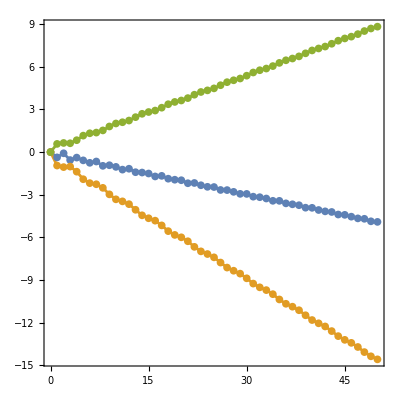

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

G=CalculateData[coin0,θ1,α1,ϕ1,t];
H=CalculateData[coin0,θ2,α2,ϕ2,t];
J=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[{G[[2]],H[[2]],J[[2]]},t,PlotLegends->{"","",""}]
```

```mathematica
ExpValVsTimeManipulate[coin0_,tmax_Integer]:=Manipulate[Module[{posProb,expecVal},
posProb=PosProbDisTime[coin0,θ,α,ϕ,t];
expecVal=ExpecValue[posProb,t];
ExpValVsTimePlot[expecVal,t]
],
{θ,0,2 Pi,Appearance->"Labeled"},
{α,0,Pi,Appearance->"Labeled"},
{ϕ,0,2 Pi,Appearance->"Labeled"}
]
```

### Valor de expectación para un tiempo fijo

```mathematica
ClearAll@FixedTimeExpValPlot
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/nα,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

```mathematica
FixedTimeExpValPlot[data_List,fixedt_Integer,initCoinState_,θ_,nα_Integer,nϕ_Integer,αLabels_Integer,ϕLabels_Integer,opts:OptionsPattern[ListDensityPlot]]:=Module[{alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{αLabels*i π/nα,ToString[TraditionalForm[αLabels*i π/nα]]},{i,0,nα}];
phiTicks=Table[{ϕLabels*i*2π/nϕ,ToString[TraditionalForm[ϕLabels*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{ColorData[{"Rainbow",{-10,10}}][#]&,{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],"     θ = ",θ,",     = ",fixedt}],
opts
]
]
```

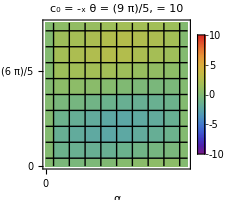

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
fixedt=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataExpVal[res,fixedt];
FixedTimeExpValPlot[data,fixedt,coin0,θ,nα,nϕ]
```

### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[data_List,initCoinState_,θ_,opts:OptionsPattern[Graphics3D]]:=Module[{sphere},
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.03],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

RGBColor["#00D52C"],Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="Indefinido"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[data,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",LabelCoinState[initCoinState],",    θ = ",θ}],
opts
]
]
```

```mathematica
coin0=minusX;
θ=9π/5;
nα=10;
nϕ=10;
t=10;
res=VaryingAlpha[coin0,θ,nα,nϕ,t];
data=ExtractDataSphereGraph[res];
SphereGraph[data,coin0,θ]
```

-Graphics3D-

### Valor de expectación contra θ

```mathematica
ExpValVsThetaPlot[coin0_,α_,ϕ_,tmax_Integer,opts:OptionsPattern[ListLinePlot]]:=Module[{thetaVals,expecVals},
thetaVals=Subdivide[0,2 π,100];

expecVals=Table[Table[ExpecValue[PosProbDisTime[coin0,θ,α,ϕ,t],t][[t+1]],{θ,thetaVals}],{t,1,tmax}];

ListLinePlot[Transpose[{thetaVals,#}]&/@expecVals,
PlotLegends->Placed[LineLegend[Range[1,tmax],
LabelStyle->{FontSize->12},
LegendLabel->Style["",FontSize->13]],
Right
],
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{Automatic,Automatic},{Table[{k π/4,ToString[TraditionalForm[k π/4]]},{k,0,8}],Automatic}},
PlotRange->{All,{-(t+0.05t),tmax+0.05tmax}},
PlotStyle->ColorData[97]/@Range[tmax],
ImageSize->350,
opts]
]
```

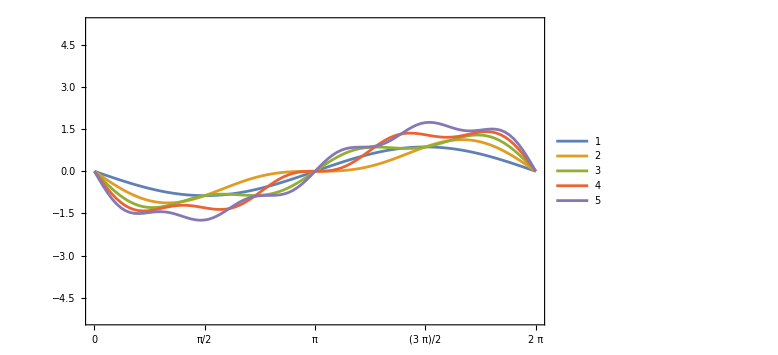

```mathematica
coin0=plusX;
α=π/2.;
ϕ=π/3.;
t=5;

ExpValVsThetaPlot[coin0,α,ϕ,t]
```

```mathematica
ClearAll@ExpValVsThetaManipulate
```

```mathematica
ExpValVsThetaManipulate[coin0_,tmax_Integer:5]:=Manipulate[
ExpValVsThetaPlot[coin0,α,ϕ,tmax],
{α,0,π,Appearance->"Labeled"},
{ϕ,0,2 π,Appearance->"Labeled"}
]
```

# Resultados

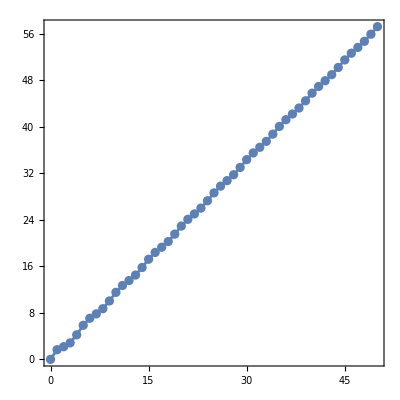

```mathematica
β=π/2.;
γ=0.7;
coin0={β,γ};

θ=π;
α=π/5.;
ϕ=π/3.;

ExpValVsTimePlot[CalculateData[coin0,θ,α,ϕ,t][[2]],t]
```

```mathematica
{β,γ}={Pi/2.,Pi/3.};
coin0=QubitState[β,γ];
t=20;
ExpValVsTimeManipulate[coin0,t]
```

```mathematica
{β,γ}={Pi/2.,Pi/3.};
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaManipulate[coin0]
```

```mathematica
3Pi/4.
```

2.35619

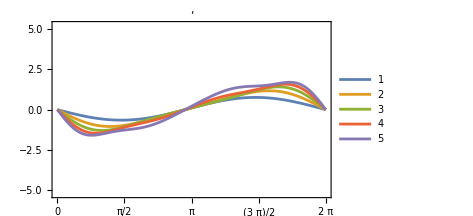

```mathematica
{α,ϕ}={Pi/4.,4Pi/5.};
{β,γ}={Pi/2.,Pi/3.};
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaPlot[coin0,α,ϕ,t,
PlotLabel->Row[{",     "}]
]
```

```mathematica
Export["/Users/gabrielaperez/Desktop/Cosas de Prácticas/quantum_walks/Mariana/EPS/Resultados/Informe/criticalAngle.pdf",%,"PDF"];
```

```mathematica
a=Pi/3.;
```

```mathematica
Rationalize[a,0]
```

26714619/25510582

```mathematica
ToString[a]
```

1.0472

```mathematica
7Pi/8.
```

2.74889

```mathematica
20Pi/21.
```

2.99199

```mathematica
2.9932255834603003
```

```mathematica
R=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

2.2638

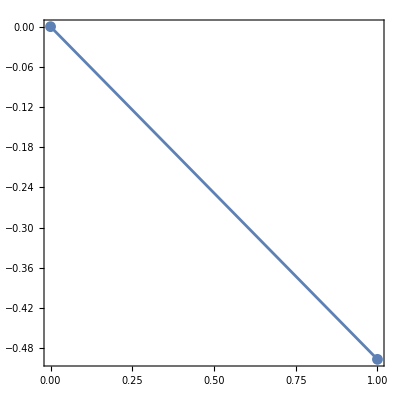

```mathematica
t=1;
coin0={β,γ};
θ=R;
ExpValVsTimePlot[CalculateData[coin0,θ,α,ϕ,t][[2]],t]
```

```mathematica
CalculateData[coin0,θ,α,ϕ,t][[2]]
```

{0,-0.496438}

```mathematica
2.4883548577
```

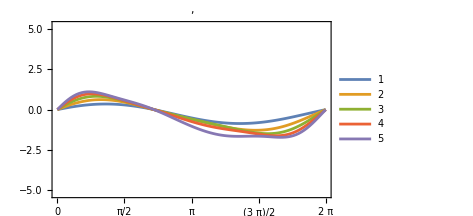

```mathematica
{α,ϕ}={11Pi/9.,4Pi/5};
{β,γ}={Pi/2.,Pi/8.};
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaPlot[coin0,α,ϕ,t,
PlotLabel->Row[{",     "}]
]
```

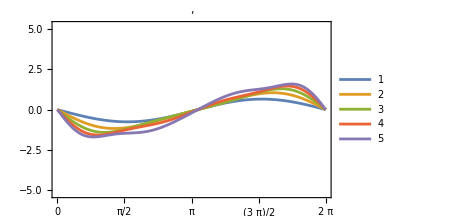

```mathematica
{α,ϕ}={3Pi/4.,4Pi/5.};
{β,γ}={Pi/2.,Pi/3.};
coin0=QubitState[β,γ];
t=5;
ExpValVsThetaPlot[coin0,α,ϕ,t,
PlotLabel->Row[{",     "}]
]
```

```mathematica
R=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

2.99323

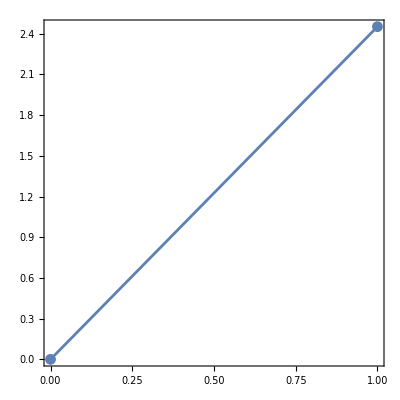

```mathematica
t=1;
coin0={β,γ};
θ=R;
ExpValVsTimePlot[CalculateData[coin0,θ,α,ϕ,t][[2]],t]
```

```mathematica
2.9932255834603003
```

```mathematica
2.993225583460301
```

# Cosas de José prueba

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QuantumWalks.wl"]
```

SetDelayed::write: Tag Charting`ScaledTicks in Charting`ScaledTicks[{TicksFunction,CustomTicks[opts:OptionsPattern[]]},sc_,Nice][_,_,_] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QMB.wl"]
```

```mathematica
CircleEq[α_,ϕ_,β_,γ_,θ_,φ_]:=Cos[α]*Cos[θ]+Sin[α]*Sin[θ]*Cos[ϕ-φ]-(Cos[α]*Cos[β]+Sin[α]*Sin[β]*Cos[ϕ-γ])
```

```mathematica
Azimuthal[ϕ_]:=Mod[ϕ+Pi,2 Pi]-Pi
```

```mathematica
{α,ϕ}={4Pi/5.,11Pi/9.};
{β,γ}={Pi/2.,Pi/8.};
```

```mathematica
CircleEq[α,ϕ,β,γ,θ,φ]==0
```

0.560581-0.809017 Cos[θ]+0.587785 Cos[3.83972-φ] Sin[θ]==0

```mathematica
θ=Pi/2.;(*intersección con el plano xy*)
φsols=φ/.#&/@Solve[CircleEq[α,ϕ,β,γ,θ,φ]==0,φ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{1.00356,6.67588}

```mathematica
ϕ+(γ-ϕ)
```

0.392699

```mathematica
ϕ-(γ-ϕ)
```

7.28675

```mathematica
(*vectores en coordenadas cartesianas de las soluciones*)
vecs=Chop@FromSphericalCoordinates[{1,Pi/2.,Azimuthal[#]}]&/@φsols
```

{{0.5373,0.843391,0},{0.92388,0.382683,0}}

```mathematica
Module[{n,circxy,sphere,blochVectorψ0},
n=FromSphericalCoordinates[{1.,α,Azimuthal[ϕ]}];(*eje de rotación*)
blochVectorψ0=Chop@FromSphericalCoordinates[{1,β,Azimuthal[γ]}];
circ2=Table[RotationMatrix[θ,n].blochVectorψ0,{θ,0,2 Pi,Pi/20}];(*rotation matrix*)
circxy=Table[{Cos[θ],Sin[θ],0},{θ,0,2 Pi,Pi/20}];(*Intersección con plano xy*)
sphere=Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]}];(*Esfera unitaria*)

Graphics3D[
{
sphere[[1]],(*Esfera*)
Red,Arrow[{{0,0,0},n}],(*rotation axis*)
Black,Style[Text["",n+0.05],FontSize->20],
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]].n*n}]},
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]]-vecs[[1]].n*n}]},
Magenta,Arrow[{{0,0,0},vecs[[1]]}],(*initial coin state*)
Black,Style[Text["",vecs[[1]]+{0,0,0.1}],FontSize->20],
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]].n*n}]},
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]]-vecs[[2]].n*n}]},
Black,Arrow[{{0,0,0},vecs[[2]]}],(*initial coin state*)
Black,Style[Text["",vecs[[2]]+{0.1,0.1,0}],FontSize->20],
Black,Style[Text["",vecs[[2]]-vecs[[2]].n*n-0.1],FontSize->20],
Black,Style[Text["",vecs[[1]]-vecs[[1]].n*n+0.1],FontSize->20],
Black,Arrow[{{0,0,0},RotationMatrix[4.084,n].blochVectorψ0}],
Blue,Line[circxy],  (*Círculo en azul*)
Orange,Line[circ2]
},
Boxed->True,
Axes->True,
AxesLabel->{"x","y","z"},
LabelStyle->Directive[Black,FontSize->15],
PlotRange->ConstantArray[{-1,1},3],
ImageSize->500
]
]
```

-Graphics3D-

```mathematica
n=FromSphericalCoordinates[{1,α,Azimuthal[ϕ]}];(*eje de rotacion*)
```

```mathematica
(*Proyección de v1 y v2 al plano que define la rotación*)
v1proj=Normalize[vecs[[1]]-vecs[[1]].n*n]
v2proj=Normalize[vecs[[2]]-vecs[[2]].n*n]
```

{0.344025,0.762701,-0.547663}

{0.810853,0.206357,-0.547663}

```mathematica
θ=ArcCos[v1proj.v2proj]
```

0.743245

```mathematica
R=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

0.743245

```mathematica
R2=2π-ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

5.53994

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*(2Pi-R)/2*(n.(Pauli/@{1,2,3}))];
```

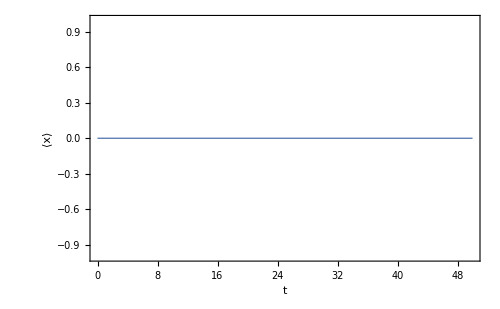

```mathematica
ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

# Cosas de José bien

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QuantumWalks.wl"]
```

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QMB.wl"]
```

```mathematica
CircleEq[α_,ϕ_,β_,γ_,θ_,φ_]:=Cos[α]*Cos[θ]+Sin[α]*Sin[θ]*Cos[ϕ-φ]-(Cos[α]*Cos[β]+Sin[α]*Sin[β]*Cos[ϕ-γ])
```

```mathematica
Azimuthal[ϕ_]:=Mod[ϕ+Pi,2 Pi]-Pi
```

```mathematica
{α,ϕ}={3Pi/4.,4Pi/5.};
{β,γ}={Pi/2.,Pi/3.};
```

```mathematica
CircleEq[α,ϕ,β,γ,θ,φ]==0
```

0.625426+0.104527 Cos[2.51327-φ]==0

```mathematica
θ=Pi/2.;(*intersección con el plano xy*)
φsols=φ/.#&/@Solve[CircleEq[α,ϕ,β,γ,θ,φ]==0,φ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{1.0472,3.97935}

```mathematica
(*vectores en coordenadas cartesianas de las soluciones*)
vecs=Chop@FromSphericalCoordinates[{1,Pi/2.,Azimuthal[#]}]&/@φsols
```

{{0.5,0.866025,0},{-0.669131,-0.743145,0}}

```mathematica
Module[{n,circxy,sphere,blochVectorψ0},
n=FromSphericalCoordinates[{1.,α,Azimuthal[ϕ]}];(*eje de rotación*)
blochVectorψ0=Chop@FromSphericalCoordinates[{1,β,Azimuthal[γ]}];
circ2=Table[RotationMatrix[θ,n].blochVectorψ0,{θ,0,2 Pi,Pi/20}];(*rotation matrix*)
circxy=Table[{Cos[θ],Sin[θ],0},{θ,0,2 Pi,Pi/20}];(*Intersección con plano xy*)
sphere=Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]}];(*Esfera unitaria*)

Graphics3D[
{
sphere[[1]],(*Esfera*)
Red,Arrow[{{0,0,0},n}],(*rotation axis*)
Black,Style[Text["",n+0.05],FontSize->20],
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]].n*n}]},
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]]-vecs[[1]].n*n}]},
Magenta,Arrow[{{0,0,0},vecs[[1]]}],(*initial coin state*)
Black,Style[Text["",vecs[[1]]+{0,0,0.1}],FontSize->20],
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]].n*n}]},
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]]-vecs[[2]].n*n}]},
Black,Arrow[{{0,0,0},vecs[[2]]}],(*initial coin state*)
Black,Style[Text["",vecs[[2]]+{0.1,0.1,0}],FontSize->20],
Black,Style[Text["",vecs[[2]]-vecs[[2]].n*n-0.1],FontSize->20],
Black,Style[Text["",vecs[[1]]-vecs[[1]].n*n+0.1],FontSize->20],
Black,Arrow[{{0,0,0},RotationMatrix[4.084,n].blochVectorψ0}],
Blue,Line[circxy],  (*Círculo en azul*)
Orange,Line[circ2]
},
Boxed->True,
Axes->True,
AxesLabel->{"x","y","z"},
LabelStyle->Directive[Black,FontSize->15],
PlotRange->ConstantArray[{-1,1},3],
ImageSize->500
]
]
```

-Graphics3D-

```mathematica
n=FromSphericalCoordinates[{1,α,Azimuthal[ϕ]}];(*eje de rotacion*)
```

```mathematica
(*Proyección de v1 y v2 al plano que define la rotación*)
v1proj=Normalize[vecs[[1]]-vecs[[1]].n*n]
v2proj=Normalize[vecs[[2]]-vecs[[2]].n*n]
```

{0.54377,0.837596,0.0524076}

{-0.628567,-0.775988,0.0524076}

```mathematica
θ=ArcCos[v1proj.v2proj]
```

2.99323

```mathematica
R=ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

2.99323

```mathematica
R2=2π-ArcCos[(Cos[2(γ-ϕ)]-Sin[α]^2 Cos[γ-ϕ]^2)/(1-Sin[α]^2 Cos[γ-ϕ]^2)]
```

3.28996

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*(2Pi-R)/2*(n.(Pauli/@{1,2,3}))];
```

```mathematica
ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

-Graphics-

# Cosas de José original

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QuantumWalks.wl"]
```

SetDelayed::write: Tag Charting`ScaledTicks in Charting`ScaledTicks[{TicksFunction,CustomTicks[opts:OptionsPattern[]]},sc_,Nice][_,_,_] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]];Get["/Users/gabrielaperez/Desktop/Cosas de Prácticas/libs/QMB.wl"]
```

```mathematica
CircleEq[α_,ϕ_,β_,γ_,θ_,φ_]:=Cos[α]*Cos[θ]+Sin[α]*Sin[θ]*Cos[ϕ-φ]-(Cos[α]*Cos[β]+Sin[α]*Sin[β]*Cos[ϕ-γ])
```

```mathematica
Azimuthal[ϕ_]:=Mod[ϕ+Pi,2 Pi]-Pi
```

```mathematica
SeedRandom[30946];
α=RandomReal[{0,Pi}]
β=Pi/2.;(*Estado inicial sobre el plano XY*)
{ϕ,γ}=RandomReal[{0,2*Pi},2]
```

0.339443

{4.12666,2.05662}

```mathematica
CircleEq[α,ϕ,β,γ,θ,φ]==0
```

0.15941+0.94294 Cos[θ]+0.332962 Cos[4.12666-φ] Sin[θ]==0

```mathematica
θ=Pi/2.;(*intersección con el plano xy*)
φsols=φ/.#&/@Solve[CircleEq[α,ϕ,β,γ,θ,φ]==0,φ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{2.05662,6.1967}

```mathematica
(*vectores en coordenadas cartesianas de las soluciones*)
vecs=Chop@FromSphericalCoordinates[{1,Pi/2.,Azimuthal[#]}]&/@φsols
```

{{-0.466936,0.884291,0},{0.996263,-0.0863745,0}}

```mathematica
Module[{n,circxy,sphere,blochVectorψ0},
n=FromSphericalCoordinates[{1.,α,Azimuthal[ϕ]}];(*eje de rotación*)
blochVectorψ0=Chop@FromSphericalCoordinates[{1,β,Azimuthal[γ]}];
circ2=Table[RotationMatrix[θ,n].blochVectorψ0,{θ,0,2 Pi,Pi/20}];(*rotation matrix*)
circxy=Table[{Cos[θ],Sin[θ],0},{θ,0,2 Pi,Pi/20}];(*Intersección con plano xy*)
sphere=Graphics3D[{Opacity[0.2],Sphere[{0,0,0},1]}];(*Esfera unitaria*)

Graphics3D[
{
sphere[[1]],(*Esfera*)
Red,Arrow[{{0,0,0},n}],(*rotation axis*)
Black,Style[Text["",n+0.05],FontSize->20],
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]].n*n}]},
{Magenta,Dashed,Arrow[{{0,0,0},vecs[[1]]-vecs[[1]].n*n}]},
Magenta,Arrow[{{0,0,0},vecs[[1]]}],(*initial coin state*)
Black,Style[Text["",vecs[[1]]+{0,0,0.1}],FontSize->20],
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]].n*n}]},
{Black,Dashed,Arrow[{{0,0,0},vecs[[2]]-vecs[[2]].n*n}]},
Black,Arrow[{{0,0,0},vecs[[2]]}],(*initial coin state*)
Black,Style[Text["",vecs[[2]]+{0.1,0.1,0}],FontSize->20],
Black,Style[Text["",vecs[[2]]-vecs[[2]].n*n-0.1],FontSize->20],
Black,Style[Text["",vecs[[1]]-vecs[[1]].n*n+0.1],FontSize->20],
Black,Arrow[{{0,0,0},RotationMatrix[4.084,n].blochVectorψ0}],
Blue,Line[circxy],  (*Círculo en azul*)
Orange,Line[circ2]
},
Boxed->True,
Axes->True,
AxesLabel->{"x","y","z"},
LabelStyle->Directive[Black,FontSize->15],
PlotRange->ConstantArray[{-1,1},3],
ImageSize->500
]
]
```

-Graphics3D-

```mathematica
n=FromSphericalCoordinates[{1,α,Azimuthal[ϕ]}];(*eje de rotacion*)
```

```mathematica
(*Proyección de v1 y v2 al plano que define la rotación*)
v1proj=Normalize[vecs[[1]]-vecs[[1]].n*n];
v2proj=Normalize[vecs[[2]]-vecs[[2]].n*n];
```

```mathematica
θ=ArcCos[v1proj.v2proj]
```

2.19169

```mathematica
ψ0=Qubit[β,γ];t=1;
c=MatrixExp[-I*(2Pi-θ)/2*(n.(Pauli/@{1,2,3}))];
```

```mathematica
ListPlot[Table[{t,Chop@ExpValPosition[DTQW[ψ0,t,c],t]},{t,0,50}],
Joined->True,
PlotStyle->Thick,
Frame->True,
FrameStyle->Directive[Black,FontSize->24],
FrameLabel->{TraditionalForm@HoldForm@t,"⟨x⟩"},
ImageSize->500
]
```

-Graphics-